```mathematica
repo = ExpandFileName[FileNameJoin[{NotebookDirectory[], ".."}]];
out = NotebookDirectory[];
cargo = FileNameJoin[{$HomeDirectory, ".cargo", "bin", "cargo"}];
```

```mathematica
commands = {
  cargo -> {"install", "--path", FileNameJoin[{repo, "wolfram-cli"}], "--force"},
  cargo -> {"wl", "build", "--release", "--examples", "-p", "wolfram-examples"}
};

res = ExternalEvaluate[
  {"Shell", "ProcessDirectory" -> repo, "ReturnType" -> "StandardOutput"},
  commands
]
```

Installing cargo-wl v0.5.0 (/Users/rdv/Wolfram/git-rust/wolfram-rust-library/wolfram-cli)

Updating crates.io index

Locking 77 packages to latest compatible versions

Adding core-foundation v0.9.4 (available: v0.10.1)

Adding env_logger v0.10.2 (available: v0.11.10)

Adding generic-array v0.14.7 (available: v0.14.9)

Adding libloading v0.8.9 (available: v0.9.0)

Adding ordered-float v3.9.2 (available: v5.3.0)

Adding sha2 v0.10.9 (available: v0.11.0)

Adding syn v1.0.109 (available: v2.0.117)

Adding windows v0.32.0 (available: v0.62.2)

Finished `release` profile [optimized] target(s) in 3.12s

Replacing /Users/rdv/.cargo/bin/cargo-wl

Replaced package `cargo-wl v0.5.0 (/Users/rdv/Wolfram/git-rust/wolfram-rust-library/wolfram-cli)` with `cargo-wl v0.5.0 (/Users/rdv/Wolfram/git-rust/wolfram-rust-library/wolfram-cli)` (executable `cargo-wl`)

Finished `release` profile [optimized] target(s) in 0.03s

/Users/rdv/Wolfram/git-rust/wolfram-rust-library/notebooks/WolframExamples-MacOSX-ARM64

{,/Users/rdv/Wolfram/git-rust/wolfram-rust-library/notebooks/WolframExamples-MacOSX-ARM64}

```mathematica
SystemOpen[Last @ res]
```

```mathematica
manifests = FileNames["*.wl", {Last @ res}, Infinity]
```

{/Users/rdv/Wolfram/git-rust/wolfram-rust-library/notebooks/WolframExamples-MacOSX-ARM64/Artifacts.wl,/Users/rdv/Wolfram/git-rust/wolfram-rust-library/notebooks/WolframExamples-MacOSX-ARM64/Functions.wl,/Users/rdv/Wolfram/git-rust/wolfram-rust-library/notebooks/WolframExamples-MacOSX-ARM64/PacletInfo.wl}

```mathematica
libs = Get@FileNameJoin[Last @ res, "Functions.wl"];
```

```mathematica
libs[["types_wxf::duplicate"]][RandomColor[]]
```

RGBColor[0.30200609914376253, 0.2724964908112453, 0.30694245630426664]

```mathematica
libs[["types_wxf::dot"]][ByteArray[{2, 3, 4}], NumericArray[{2, 3, 4}, "Real64"]]
```

29.

```mathematica
libs[["types_native::dot"]][NumericArray[{2, 3, 4}, "Real64"], NumericArray[{2, 3, 4}, "Real64"]]
```

29.

```mathematica
libs[["types_wstp::dot"]][NumericArray[{2, 3, 4}, "Real64"], NumericArray[{2, 3, 4}, "Real64"]]
```

Failure[…]

```mathematica
libs[["types_wxf::echo_point"]][{1,2}]
```

<|x→1.,y→2.|>

```mathematica
libs[["types_wxf::echo_point"]][<|"x" -> 2|>]
```

Failure[…]

```mathematica
libs[["types_wxf::echo_point"]][<|"x" -> 2, "y" -> 3|>]
```

<|x→2.,y→3.|>

```mathematica
libs[["types_wxf::echo_point"]][NumericArray[{1, 2, 3}, "Integer64"]]
```

Failure[…]

```mathematica
libs[["types_wxf::echo_point"]][NumericArray[{1, 2}, "Real64"]]
```

<|x→1.,y→2.|>

```mathematica
libs[["types_wxf::echo_point"]][<|"y" -> 2, "x"->2|>]
```

<|x→2.,y→2.|>

# benchmark

Finished `release` profile [optimized] target(s) in 0.03s

/Users/rdv/Wolfram/git-rust/wolfram-rust-library/notebooks/WolframExamples-MacOSX-ARM64

Benchmarking add...

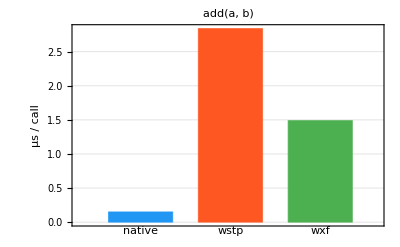

Benchmarking duplicate...

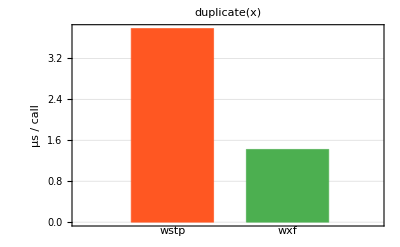

Benchmarking echo_point...

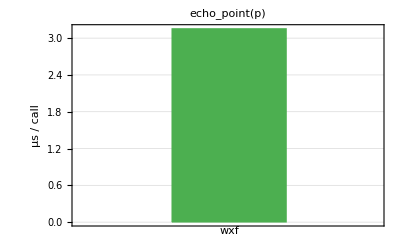

Benchmarking dot...

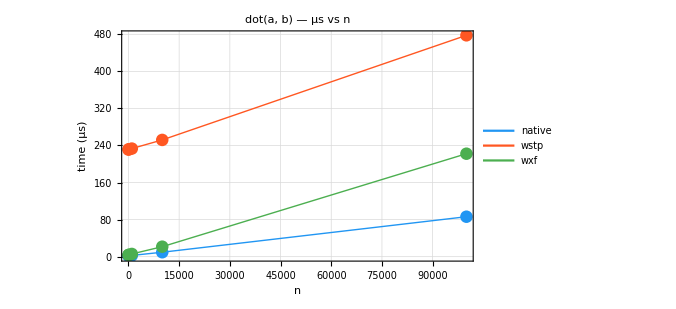

Benchmarking scale_array...

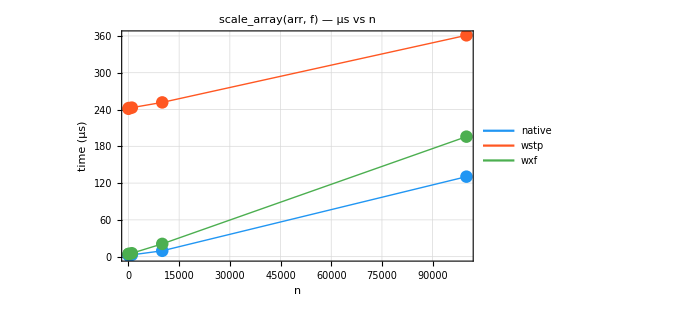

Benchmarking echo_dataset...

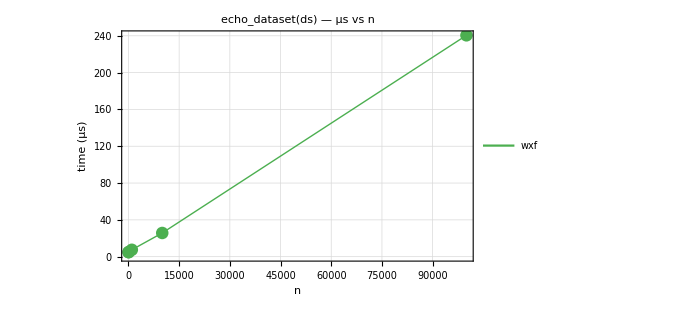

Done.

```mathematica
Get @ FileNameJoin[NotebookDirectory[], "benchmark.wl"]
```